```mathematica
SetDirectory[NotebookDirectory[]];
<<"rotationtools.wl"
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"tools2R.wl"
```

```mathematica
(*The generalised coordinates are*)
```

```mathematica
qtr = List[{θ1[t], θ2[t]}];
dqtr = D[qtr,t];
q = List/@{θ1[t], θ2[t]};
dq = D[q,t];
```

```mathematica
(*The coordinates of the center of masses of the links*)
```

```mathematica
com1 = {r1*Cos[θ1[t]], r1*Sin[θ1[t]]};
com2 = {l1*Cos[θ1[t]]+r2*Cos[θ1[t]+θ2[t]], l1*Sin[θ1[t]]+r2*Sin[θ1[t]+θ2[t]]};
com3 = {l1*Cos[θ1[t]]+l2*Cos[θ1[t]+θ2[t]], l1*Sin[θ1[t]]+l2*Sin[θ1[t]+θ2[t]]};
```

```mathematica
rot1 = rotZ[θ1[t]];
rot2 = rotZ[θ1[t]+θ2[t]];
```

```mathematica
(*Finding Jacobians of the respective center of masses of each link*)
```

```mathematica
Jcom1 = Transpose[{D[com1 , θ1[t]], D[com1, θ2[t]]}];
Jcom2 = Transpose[{D[com2, θ1[t]], D[com2, θ2[t]]}];
Jcom3 = Transpose[{D[com3, θ1[t]], D[com3, θ2[t]]}];
Jcom1w = omegaJacobianBodyFixed[rot1,{θ1[t],θ2[t]}];
Jcom2w = omegaJacobianBodyFixed[rot2,{θ1[t],θ2[t]}];
```

```mathematica
(*The kinetic energy due to linear velocities are*)
```

```mathematica
Tl = 0.5*m1*dqtr.Transpose[Jcom1].Jcom1.dq+0.5*m2*dqtr.Transpose[Jcom2].Jcom2.dq+0.5*m3*dqtr.Transpose[Jcom3].Jcom3.dq;
```

```mathematica
(*Moment of intertias of the links are I1, I2, I3. Angular velocities are ω1, ω2.*)
```

```mathematica
Ta = 0.5*I1*dqtr.Transpose[Jcom1w].Jcom1w.dq+0.5*I2*dqtr.Transpose[Jcom2w].Jcom2w.dq;
```

```mathematica
(*Total kinetic energy is*)
```

```mathematica
T = Tl+Ta;
```

```mathematica
(*Potential Energy is*)
```

```mathematica
V = m1*g*r1*Sin[θ1[t]]+m2*g*(l1*Sin[θ1[t]]+r2*Sin[θ1[t]+θ2[t]]);
```

```mathematica
(*Formulating the Lagrangian*)
```

```mathematica
L = T-V;
```

```mathematica
(*Applying Euler Lagrange equation*)
```

```mathematica
eq1d = D[D[L,D[θ1[t],t]],t]-D[L,θ1[t]];
eq2d = D[D[L,D[θ2[t],t]],t]-D[L,θ2[t]];
```

```mathematica
Collect[FullSimplify[eq1],{θ1''[t], θ1'[t],θ1[t]}]
```

eq1

```mathematica
(*Now writing the same equation of motion in Mass matrix method*)
```

```mathematica
G = {D[V,θ1[t]],D[V,θ2[t]]};
M =m1*Transpose[Jcom1].Jcom1+m2*Transpose[Jcom2].Jcom2+m3*Transpose[Jcom3].Jcom3+ I1*Transpose[Jcom1w].Jcom1w+I2*Transpose[Jcom2w].Jcom2w;
```

```mathematica
(*Now to find the isotropic conditions of the 2R manipulator*)
```

```mathematica
singular = FullSimplify[Transpose[Jcom3].Jcom3]
```

{{l1^2+l2^2+2 l1 l2 Cos[θ2[t]],l2 (l2+l1 Cos[θ2[t]])},{l2 (l2+l1 Cos[θ2[t]]),l2^2}}

```mathematica
eq1i = singular[[1,1]]-singular[[2,2]]
eq2i = singular[[1,2]]
```

l1^2+2 l1 l2 Cos[θ2[t]]

l2 (l2+l1 Cos[θ2[t]])

```mathematica
(*Condition for isotropy for the 2R planar manipulator*)
```

```mathematica
Solve[{eq1i==0,eq2i==0},{θ2[t],l2}]
```

{{l2→-l1/(√2),θ2[t]→ConditionalExpression[-π/4+2 π C[1],C[1]∈Integers]},{l2→-l1/(√2),θ2[t]→ConditionalExpression[π/4+2 π C[1],C[1]∈Integers]},{l2→l1/(√2),θ2[t]→ConditionalExpression[-(3 π)/4+2 π C[1],C[1]∈Integers]},{l2→l1/(√2),θ2[t]→ConditionalExpression[(3 π)/4+2 π C[1],C[1]∈Integers]}}

```mathematica
(*Singalurities of the 2R planar manipulator*)
```

```mathematica
angles = ik2R[{x0,y0},l1,l2,{x1,y1}]
```

{{{ArcCos[-(l1^2-l2^2+x0^2-2 x0 x1+x1^2+y0^2-2 y0 y1+y1^2)/(√(4 l1^2 (x0-x1)^2+4 l1^2 (y0-y1)^2))]+ArcTan[2 l1 (x0-x1),2 l1 (y0-y1)]},{-ArcCos[-(l1^2-l2^2+x0^2-2 x0 x1+x1^2+y0^2-2 y0 y1+y1^2)/(√(4 l1^2 (x0-x1)^2+4 l1^2 (y0-y1)^2))]+ArcTan[2 l1 (x0-x1),2 l1 (y0-y1)]}},{{{ArcTan[-x0+x1-l1 Cos[ArcCos[-(l1^2-l2^2+x0^2-2 x0 x1+x1^2+y0^2-2 y0 y1+y1^2)/(√(4 l1^2 (x0-x1)^2+4 l1^2 (y0-y1)^2))]+ArcTan[2 l1 (x0-x1),2 l1 (y0-y1)]],-y0+y1-l1 Sin[ArcCos[-(l1^2-l2^2+x0^2-2 x0 x1+x1^2+y0^2-2 y0 y1+y1^2)/(√(4 l1^2 (x0-x1)^2+4 l1^2 (y0-y1)^2))]+ArcTan[2 l1 (x0-x1),2 l1 (y0-y1)]]]}},{{ArcTan[-x0+x1-l1 Cos[ArcCos[-(l1^2-l2^2+x0^2-2 x0 x1+x1^2+y0^2-2 y0 y1+y1^2)/(√(4 l1^2 (x0-x1)^2+4 l1^2 (y0-y1)^2))]-ArcTan[2 l1 (x0-x1),2 l1 (y0-y1)]],-y0+y1+l1 Sin[ArcCos[-(l1^2-l2^2+x0^2-2 x0 x1+x1^2+y0^2-2 y0 y1+y1^2)/(√(4 l1^2 (x0-x1)^2+4 l1^2 (y0-y1)^2))]-ArcTan[2 l1 (x0-x1),2 l1 (y0-y1)]]]}}}}

```mathematica
FullSimplify[-1≤ -(l1^2-l2^2+x0^2-2 x0 x1+x1^2+y0^2-2 y0 y1+y1^2)/(√(4 l1^2 (x0-x1)^2+4 l1^2 (y0-y1)^2))≤1]
```

-1≤(-l1^2+l2^2-(x0-x1)^2-(y0-y1)^2)/(2 √(l1^2 ((x0-x1)^2+(y0-y1)^2)))≤1

Therefore from this we can see that the donimator becomes zero if x0=x1 and y0 = y1 or in other words if the manipulators end effectors reach its ground point. Also note that it becomes non existant if, 
(x0-x1)^2+(y0-y1)^2<=l1^2-l2^2, (x0-x1)^2+(y0-y1)^2>=l1^2+l2^2. These represent the singular cases. Also note that if links l1 becoming zero represents a non existant case.

```mathematica
(*Optimizing the 2R manipulators link lengths based on the global conditioning index*)
```

```mathematica
(*Writing the measure of manipulability of the manipulator using Nakamura and Yoshikawa convention*)
```

```mathematica
MoM = Simplify[Sqrt[Det[Jcom2.Transpose[Jcom2]]]]/.r2->l2/2
```

1/2 √(l1^2 l2^2 Sin[θ2[t]]^2)

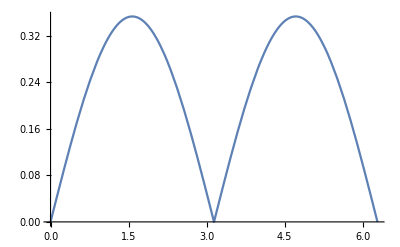

```mathematica
Plot[MoM/.{l1->1, l2->1/Sqrt[2]},{θ2[t], 0, 2π}]
```

```mathematica
T
```

{{0.5 I1 θ1'[t]^2+0.5 m1 θ1'[t] (r1^2 Cos[θ1[t]]^2 θ1'[t]+r1^2 Sin[θ1[t]]^2 θ1'[t])+0.5 I2 (θ1'[t] (θ1'[t]+θ2'[t])+θ2'[t] (θ1'[t]+θ2'[t]))+0.5 m3 (θ2'[t] (l2 Cos[θ1[t]+θ2[t]] ((l1 Cos[θ1[t]]+l2 Cos[θ1[t]+θ2[t]]) θ1'[t]+l2 Cos[θ1[t]+θ2[t]] θ2'[t])-l2 Sin[θ1[t]+θ2[t]] ((-l1 Sin[θ1[t]]-l2 Sin[θ1[t]+θ2[t]]) θ1'[t]-l2 Sin[θ1[t]+θ2[t]] θ2'[t]))+θ1'[t] ((l1 Cos[θ1[t]]+l2 Cos[θ1[t]+θ2[t]]) ((l1 Cos[θ1[t]]+l2 Cos[θ1[t]+θ2[t]]) θ1'[t]+l2 Cos[θ1[t]+θ2[t]] θ2'[t])+(-l1 Sin[θ1[t]]-l2 Sin[θ1[t]+θ2[t]]) ((-l1 Sin[θ1[t]]-l2 Sin[θ1[t]+θ2[t]]) θ1'[t]-l2 Sin[θ1[t]+θ2[t]] θ2'[t])))+0.5 m2 (θ2'[t] (r2 Cos[θ1[t]+θ2[t]] ((l1 Cos[θ1[t]]+r2 Cos[θ1[t]+θ2[t]]) θ1'[t]+r2 Cos[θ1[t]+θ2[t]] θ2'[t])-r2 Sin[θ1[t]+θ2[t]] ((-l1 Sin[θ1[t]]-r2 Sin[θ1[t]+θ2[t]]) θ1'[t]-r2 Sin[θ1[t]+θ2[t]] θ2'[t]))+θ1'[t] ((l1 Cos[θ1[t]]+r2 Cos[θ1[t]+θ2[t]]) ((l1 Cos[θ1[t]]+r2 Cos[θ1[t]+θ2[t]]) θ1'[t]+r2 Cos[θ1[t]+θ2[t]] θ2'[t])+(-l1 Sin[θ1[t]]-r2 Sin[θ1[t]+θ2[t]]) ((-l1 Sin[θ1[t]]-r2 Sin[θ1[t]+θ2[t]]) θ1'[t]-r2 Sin[θ1[t]+θ2[t]] θ2'[t])))}}

```mathematica
der = {dT1, dT2}
dertr = List[{dT1, dT2}]
```

{dT1,dT2}

{{dT1,dT2}}

```mathematica
Tlmat = 0.5*m1*dertr.Transpose[Jcom1].Jcom1.der+0.5*m2*dertr.Transpose[Jcom2].Jcom2.der+0.5*m3*dertr.Transpose[Jcom3].Jcom3.der
```

{0.5 dT1 m1 (dT1 r1^2 Cos[θ1[t]]^2+dT1 r1^2 Sin[θ1[t]]^2)+0.5 m3 (dT2 (l2 Cos[θ1[t]+θ2[t]] (dT2 l2 Cos[θ1[t]+θ2[t]]+dT1 (l1 Cos[θ1[t]]+l2 Cos[θ1[t]+θ2[t]]))-l2 Sin[θ1[t]+θ2[t]] (-dT2 l2 Sin[θ1[t]+θ2[t]]+dT1 (-l1 Sin[θ1[t]]-l2 Sin[θ1[t]+θ2[t]])))+dT1 ((l1 Cos[θ1[t]]+l2 Cos[θ1[t]+θ2[t]]) (dT2 l2 Cos[θ1[t]+θ2[t]]+dT1 (l1 Cos[θ1[t]]+l2 Cos[θ1[t]+θ2[t]]))+(-l1 Sin[θ1[t]]-l2 Sin[θ1[t]+θ2[t]]) (-dT2 l2 Sin[θ1[t]+θ2[t]]+dT1 (-l1 Sin[θ1[t]]-l2 Sin[θ1[t]+θ2[t]]))))+0.5 m2 (dT2 (r2 Cos[θ1[t]+θ2[t]] (dT2 r2 Cos[θ1[t]+θ2[t]]+dT1 (l1 Cos[θ1[t]]+r2 Cos[θ1[t]+θ2[t]]))-r2 Sin[θ1[t]+θ2[t]] (-dT2 r2 Sin[θ1[t]+θ2[t]]+dT1 (-l1 Sin[θ1[t]]-r2 Sin[θ1[t]+θ2[t]])))+dT1 ((l1 Cos[θ1[t]]+r2 Cos[θ1[t]+θ2[t]]) (dT2 r2 Cos[θ1[t]+θ2[t]]+dT1 (l1 Cos[θ1[t]]+r2 Cos[θ1[t]+θ2[t]]))+(-l1 Sin[θ1[t]]-r2 Sin[θ1[t]+θ2[t]]) (-dT2 r2 Sin[θ1[t]+θ2[t]]+dT1 (-l1 Sin[θ1[t]]-r2 Sin[θ1[t]+θ2[t]]))))}

```mathematica
Tamat = 0.5*I1*dertr.Transpose[Jcom1w].Jcom1w.der+0.5*I2*dertr.Transpose[Jcom2w].Jcom2w.der
```

{0.5 dT1^2 I1+0.5 (dT1 (dT1+dT2)+dT2 (dT1+dT2)) I2}

```mathematica
Tmat  = Tamat+Tlmat
```

{0.5 dT1^2 I1+0.5 (dT1 (dT1+dT2)+dT2 (dT1+dT2)) I2+0.5 dT1 m1 (dT1 r1^2 Cos[θ1[t]]^2+dT1 r1^2 Sin[θ1[t]]^2)+0.5 m3 (dT2 (l2 Cos[θ1[t]+θ2[t]] (dT2 l2 Cos[θ1[t]+θ2[t]]+dT1 (l1 Cos[θ1[t]]+l2 Cos[θ1[t]+θ2[t]]))-l2 Sin[θ1[t]+θ2[t]] (-dT2 l2 Sin[θ1[t]+θ2[t]]+dT1 (-l1 Sin[θ1[t]]-l2 Sin[θ1[t]+θ2[t]])))+dT1 ((l1 Cos[θ1[t]]+l2 Cos[θ1[t]+θ2[t]]) (dT2 l2 Cos[θ1[t]+θ2[t]]+dT1 (l1 Cos[θ1[t]]+l2 Cos[θ1[t]+θ2[t]]))+(-l1 Sin[θ1[t]]-l2 Sin[θ1[t]+θ2[t]]) (-dT2 l2 Sin[θ1[t]+θ2[t]]+dT1 (-l1 Sin[θ1[t]]-l2 Sin[θ1[t]+θ2[t]]))))+0.5 m2 (dT2 (r2 Cos[θ1[t]+θ2[t]] (dT2 r2 Cos[θ1[t]+θ2[t]]+dT1 (l1 Cos[θ1[t]]+r2 Cos[θ1[t]+θ2[t]]))-r2 Sin[θ1[t]+θ2[t]] (-dT2 r2 Sin[θ1[t]+θ2[t]]+dT1 (-l1 Sin[θ1[t]]-r2 Sin[θ1[t]+θ2[t]])))+dT1 ((l1 Cos[θ1[t]]+r2 Cos[θ1[t]+θ2[t]]) (dT2 r2 Cos[θ1[t]+θ2[t]]+dT1 (l1 Cos[θ1[t]]+r2 Cos[θ1[t]+θ2[t]]))+(-l1 Sin[θ1[t]]-r2 Sin[θ1[t]+θ2[t]]) (-dT2 r2 Sin[θ1[t]+θ2[t]]+dT1 (-l1 Sin[θ1[t]]-r2 Sin[θ1[t]+θ2[t]]))))}

```mathematica
ToMatlab[{0.5 dT1^2 I1+0.5 (dT1 (dT1+dT2)+dT2 (dT1+dT2)) I2+0.5 dT1 m1 (dT1 r1^2 Cos[t1]^2+dT1 r1^2 Sin[t1]^2)+0.5 m3 (dT2 (l2 Cos[t1+t2] (dT2 l2 Cos[t1+t2]+dT1 (l1 Cos[t1]+l2 Cos[t1+t2]))-l2 Sin[t1+t2] (-dT2 l2 Sin[t1+t2]+dT1 (-l1 Sin[t1]-l2 Sin[t1+t2])))+dT1 ((l1 Cos[t1]+l2 Cos[t1+t2]) (dT2 l2 Cos[t1+t2]+dT1 (l1 Cos[t1]+l2 Cos[t1+t2]))+(-l1 Sin[t1]-l2 Sin[t1+t2]) (-dT2 l2 Sin[t1+t2]+dT1 (-l1 Sin[t1]-l2 Sin[t1+t2]))))+0.5 m2 (dT2 (r2 Cos[t1+t2] (dT2 r2 Cos[t1+t2]+dT1 (l1 Cos[t1]+r2 Cos[t1+t2]))-r2 Sin[t1+t2] (-dT2 r2 Sin[t1+t2]+dT1 (-l1 Sin[t1]-r2 Sin[t1+t2])))+dT1 ((l1 Cos[t1]+r2 Cos[t1+t2]) (dT2 r2 Cos[t1+t2]+dT1 (l1 Cos[t1]+r2 Cos[t1+t2]))+(-l1 Sin[t1]-r2 Sin[t1+t2]) (-dT2 r2 Sin[t1+t2]+dT1 (-l1 Sin[t1]-r2 Sin[t1+t2]))))}]
```

[0.5E0.*dT1.^2.*I1+0.5E0.*(dT1.*(dT1+dT2)+dT2.*(dT1+dT2)).*I2+ ...
  0.5E0.*dT1.*m1.*(dT1.*r1.^2.*cos(t1).^2+dT1.*r1.^2.*sin(t1).^2)+ ...
  0.5E0.*m3.*(dT2.*(l2.*cos(t1+t2).*(dT2.*l2.*cos(t1+t2)+dT1.*(l1.* ...
  cos(t1)+l2.*cos(t1+t2)))+(-1).*l2.*sin(t1+t2).*((-1).*dT2.*l2.* ...
  sin(t1+t2)+dT1.*((-1).*l1.*sin(t1)+(-1).*l2.*sin(t1+t2))))+dT1.*(( ...
  l1.*cos(t1)+l2.*cos(t1+t2)).*(dT2.*l2.*cos(t1+t2)+dT1.*(l1.*cos( ...
  t1)+l2.*cos(t1+t2)))+((-1).*l1.*sin(t1)+(-1).*l2.*sin(t1+t2)).*(( ...
  -1).*dT2.*l2.*sin(t1+t2)+dT1.*((-1).*l1.*sin(t1)+(-1).*l2.*sin(t1+ ...
  t2)))))+0.5E0.*m2.*(dT2.*(r2.*cos(t1+t2).*(dT2.*r2.*cos(t1+t2)+ ...
  dT1.*(l1.*cos(t1)+r2.*cos(t1+t2)))+(-1).*r2.*sin(t1+t2).*((-1).* ...
  dT2.*r2.*sin(t1+t2)+dT1.*((-1).*l1.*sin(t1)+(-1).*r2.*sin(t1+t2))) ...
  )+dT1.*((l1.*cos(t1)+r2.*cos(t1+t2)).*(dT2.*r2.*cos(t1+t2)+dT1.*( ...
  l1.*cos(t1)+r2.*cos(t1+t2)))+((-1).*l1.*sin(t1)+(-1).*r2.*sin(t1+ ...
  t2)).*((-1).*dT2.*r2.*sin(t1+t2)+dT1.*((-1).*l1.*sin(t1)+(-1).* ...
  r2.*sin(t1+t2)))))];

```mathematica
M
```

{{I1+I2+m1 (r1^2 Cos[θ1[t]]^2+r1^2 Sin[θ1[t]]^2)+m3 ((l1 Cos[θ1[t]]+l2 Cos[θ1[t]+θ2[t]])^2+(-l1 Sin[θ1[t]]-l2 Sin[θ1[t]+θ2[t]])^2)+m2 ((l1 Cos[θ1[t]]+r2 Cos[θ1[t]+θ2[t]])^2+(-l1 Sin[θ1[t]]-r2 Sin[θ1[t]+θ2[t]])^2),I2+m3 (l2 Cos[θ1[t]+θ2[t]] (l1 Cos[θ1[t]]+l2 Cos[θ1[t]+θ2[t]])-l2 Sin[θ1[t]+θ2[t]] (-l1 Sin[θ1[t]]-l2 Sin[θ1[t]+θ2[t]]))+m2 (r2 Cos[θ1[t]+θ2[t]] (l1 Cos[θ1[t]]+r2 Cos[θ1[t]+θ2[t]])-r2 Sin[θ1[t]+θ2[t]] (-l1 Sin[θ1[t]]-r2 Sin[θ1[t]+θ2[t]]))},{I2+m3 (l2 Cos[θ1[t]+θ2[t]] (l1 Cos[θ1[t]]+l2 Cos[θ1[t]+θ2[t]])-l2 Sin[θ1[t]+θ2[t]] (-l1 Sin[θ1[t]]-l2 Sin[θ1[t]+θ2[t]]))+m2 (r2 Cos[θ1[t]+θ2[t]] (l1 Cos[θ1[t]]+r2 Cos[θ1[t]+θ2[t]])-r2 Sin[θ1[t]+θ2[t]] (-l1 Sin[θ1[t]]-r2 Sin[θ1[t]+θ2[t]])),I2+m3 (l2^2 Cos[θ1[t]+θ2[t]]^2+l2^2 Sin[θ1[t]+θ2[t]]^2)+m2 (r2^2 Cos[θ1[t]+θ2[t]]^2+r2^2 Sin[θ1[t]+θ2[t]]^2)}}

```mathematica
M-Transpose[M]
```

{{0,0},{0,0}}

```mathematica
q = {θ1[t], θ2[t]};
```

```mathematica
n = Length[q];
tempC = Table[0, {ii, 1,n}, {jj, 1,n}];
For [ii = 1, ii ≤ n, 
For[jj = 1, jj ≤ n,
For[kk = 1, kk≤ n, 
tempC[[ii,jj]] +=1/2*( D[M[[ii,jj]], q[[kk]]] + D[M[[ii,kk]], q[[jj]]] - D[M[[jj, kk]], q[[ii]]])*D[q[[kk]],t] ;
kk++];
jj++];
ii++];
```

```mathematica
Cmat = FullSimplify[tempC]
```

{{-l1 (l2 m3+m2 r2) Sin[θ2[t]] θ2'[t],-l1 (l2 m3+m2 r2) Sin[θ2[t]] (θ1'[t]+θ2'[t])},{l1 (l2 m3+m2 r2) Sin[θ2[t]] θ1'[t],0}}

```mathematica
A = FullSimplify[D[M,t] - 2*Cmat];
MatrixForm[A+ Transpose[A]]
```

(0 | 0
0 | 0)

```mathematica
G
```

{g m1 r1 Cos[θ1[t]]+g m2 (l1 Cos[θ1[t]]+r2 Cos[θ1[t]+θ2[t]]),g m2 r2 Cos[θ1[t]+θ2[t]]}

```mathematica
d2q = D[D[q,t],t]
```

{θ1''[t],θ2''[t]}

```mathematica
dq
```

{{θ1'[t]},{θ2'[t]}}

```mathematica
q
```

{θ1[t],θ2[t]}

```mathematica
Dynamics = M.d2q+Cmat.dq+G
```

{{g m1 r1 Cos[θ1[t]]+g m2 (l1 Cos[θ1[t]]+r2 Cos[θ1[t]+θ2[t]])-l1 (l2 m3+m2 r2) Sin[θ2[t]] θ1'[t] θ2'[t]-l1 (l2 m3+m2 r2) Sin[θ2[t]] θ2'[t] (θ1'[t]+θ2'[t])+(I1+I2+m1 (r1^2 Cos[θ1[t]]^2+r1^2 Sin[θ1[t]]^2)+m3 ((l1 Cos[θ1[t]]+l2 Cos[θ1[t]+θ2[t]])^2+(-l1 Sin[θ1[t]]-l2 Sin[θ1[t]+θ2[t]])^2)+m2 ((l1 Cos[θ1[t]]+r2 Cos[θ1[t]+θ2[t]])^2+(-l1 Sin[θ1[t]]-r2 Sin[θ1[t]+θ2[t]])^2)) θ1''[t]+(I2+m3 (l2 Cos[θ1[t]+θ2[t]] (l1 Cos[θ1[t]]+l2 Cos[θ1[t]+θ2[t]])-l2 Sin[θ1[t]+θ2[t]] (-l1 Sin[θ1[t]]-l2 Sin[θ1[t]+θ2[t]]))+m2 (r2 Cos[θ1[t]+θ2[t]] (l1 Cos[θ1[t]]+r2 Cos[θ1[t]+θ2[t]])-r2 Sin[θ1[t]+θ2[t]] (-l1 Sin[θ1[t]]-r2 Sin[θ1[t]+θ2[t]]))) θ2''[t]},{g m2 r2 Cos[θ1[t]+θ2[t]]+l1 (l2 m3+m2 r2) Sin[θ2[t]] θ1'[t]^2+(I2+m3 (l2 Cos[θ1[t]+θ2[t]] (l1 Cos[θ1[t]]+l2 Cos[θ1[t]+θ2[t]])-l2 Sin[θ1[t]+θ2[t]] (-l1 Sin[θ1[t]]-l2 Sin[θ1[t]+θ2[t]]))+m2 (r2 Cos[θ1[t]+θ2[t]] (l1 Cos[θ1[t]]+r2 Cos[θ1[t]+θ2[t]])-r2 Sin[θ1[t]+θ2[t]] (-l1 Sin[θ1[t]]-r2 Sin[θ1[t]+θ2[t]]))) θ1''[t]+(I2+m3 (l2^2 Cos[θ1[t]+θ2[t]]^2+l2^2 Sin[θ1[t]+θ2[t]]^2)+m2 (r2^2 Cos[θ1[t]+θ2[t]]^2+r2^2 Sin[θ1[t]+θ2[t]]^2)) θ2''[t]}}

```mathematica
Dynamics[[1]]
```

{g m1 r1 Cos[θ1[t]]+g m2 (l1 Cos[θ1[t]]+r2 Cos[θ1[t]+θ2[t]])-l1 (l2 m3+m2 r2) Sin[θ2[t]] θ1'[t] θ2'[t]-l1 (l2 m3+m2 r2) Sin[θ2[t]] θ2'[t] (θ1'[t]+θ2'[t])+(I1+I2+m1 (r1^2 Cos[θ1[t]]^2+r1^2 Sin[θ1[t]]^2)+m3 ((l1 Cos[θ1[t]]+l2 Cos[θ1[t]+θ2[t]])^2+(-l1 Sin[θ1[t]]-l2 Sin[θ1[t]+θ2[t]])^2)+m2 ((l1 Cos[θ1[t]]+r2 Cos[θ1[t]+θ2[t]])^2+(-l1 Sin[θ1[t]]-r2 Sin[θ1[t]+θ2[t]])^2)) θ1''[t]+(I2+m3 (l2 Cos[θ1[t]+θ2[t]] (l1 Cos[θ1[t]]+l2 Cos[θ1[t]+θ2[t]])-l2 Sin[θ1[t]+θ2[t]] (-l1 Sin[θ1[t]]-l2 Sin[θ1[t]+θ2[t]]))+m2 (r2 Cos[θ1[t]+θ2[t]] (l1 Cos[θ1[t]]+r2 Cos[θ1[t]+θ2[t]])-r2 Sin[θ1[t]+θ2[t]] (-l1 Sin[θ1[t]]-r2 Sin[θ1[t]+θ2[t]]))) θ2''[t]}

```mathematica
Dynamics[[2]]
```

{g m2 r2 Cos[θ1[t]+θ2[t]]+l1 (l2 m3+m2 r2) Sin[θ2[t]] θ1'[t]^2+(I2+m3 (l2 Cos[θ1[t]+θ2[t]] (l1 Cos[θ1[t]]+l2 Cos[θ1[t]+θ2[t]])-l2 Sin[θ1[t]+θ2[t]] (-l1 Sin[θ1[t]]-l2 Sin[θ1[t]+θ2[t]]))+m2 (r2 Cos[θ1[t]+θ2[t]] (l1 Cos[θ1[t]]+r2 Cos[θ1[t]+θ2[t]])-r2 Sin[θ1[t]+θ2[t]] (-l1 Sin[θ1[t]]-r2 Sin[θ1[t]+θ2[t]]))) θ1''[t]+(I2+m3 (l2^2 Cos[θ1[t]+θ2[t]]^2+l2^2 Sin[θ1[t]+θ2[t]]^2)+m2 (r2^2 Cos[θ1[t]+θ2[t]]^2+r2^2 Sin[θ1[t]+θ2[t]]^2)) θ2''[t]}

```mathematica
Solve[{FullSimplify[Dynamics[[1]]]==0,FullSimplify[Dynamics[[2]]]==0},{θ1''[t],θ2''[t]}]
```

{{θ1''[t]→-((-(I2+l2^2 m3+m2 r2^2+l1 (l2 m3+m2 r2) Cos[θ2[t]]) (g m2 r2 Cos[θ1[t]+θ2[t]]+l1 (l2 m3+m2 r2) Sin[θ2[t]] θ1'[t]^2)+(I2+l2^2 m3+m2 r2^2) (g (l1 m2+m1 r1) Cos[θ1[t]]+g m2 r2 Cos[θ1[t]+θ2[t]]-2 l1 (l2 m3+m2 r2) Sin[θ2[t]] θ1'[t] θ2'[t]-l1 (l2 m3+m2 r2) Sin[θ2[t]] θ2'[t]^2))/(-(I2+l2^2 m3+m2 r2^2+l1 (l2 m3+m2 r2) Cos[θ2[t]])^2+(I2+l2^2 m3+m2 r2^2) (I1+I2+l2^2 m3+l1^2 (m2+m3)+m1 r1^2+m2 r2^2+2 l1 (l2 m3+m2 r2) Cos[θ2[t]]))),θ2''[t]→-((-g I2 l1 m2 Cos[θ1[t]]-g l1 l2^2 m2 m3 Cos[θ1[t]]-g I2 m1 r1 Cos[θ1[t]]-g l2^2 m1 m3 r1 Cos[θ1[t]]-g l1 m2^2 r2^2 Cos[θ1[t]]-g m1 m2 r1 r2^2 Cos[θ1[t]]-g l1^2 l2 m2 m3 Cos[θ1[t]] Cos[θ2[t]]-g l1 l2 m1 m3 r1 Cos[θ1[t]] Cos[θ2[t]]-g l1^2 m2^2 r2 Cos[θ1[t]] Cos[θ2[t]]-g l1 m1 m2 r1 r2 Cos[θ1[t]] Cos[θ2[t]]+g I1 m2 r2 Cos[θ1[t]+θ2[t]]+g l1^2 m2^2 r2 Cos[θ1[t]+θ2[t]]+g l1^2 m2 m3 r2 Cos[θ1[t]+θ2[t]]+g m1 m2 r1^2 r2 Cos[θ1[t]+θ2[t]]+g l1 l2 m2 m3 r2 Cos[θ2[t]] Cos[θ1[t]+θ2[t]]+g l1 m2^2 r2^2 Cos[θ2[t]] Cos[θ1[t]+θ2[t]]+I1 l1 l2 m3 Sin[θ2[t]] θ1'[t]^2+I2 l1 l2 m3 Sin[θ2[t]] θ1'[t]^2+l1^3 l2 m2 m3 Sin[θ2[t]] θ1'[t]^2+l1^3 l2 m3^2 Sin[θ2[t]] θ1'[t]^2+l1 l2^3 m3^2 Sin[θ2[t]] θ1'[t]^2+l1 l2 m1 m3 r1^2 Sin[θ2[t]] θ1'[t]^2+I1 l1 m2 r2 Sin[θ2[t]] θ1'[t]^2+I2 l1 m2 r2 Sin[θ2[t]] θ1'[t]^2+l1^3 m2^2 r2 Sin[θ2[t]] θ1'[t]^2+l1^3 m2 m3 r2 Sin[θ2[t]] θ1'[t]^2+l1 l2^2 m2 m3 r2 Sin[θ2[t]] θ1'[t]^2+l1 m1 m2 r1^2 r2 Sin[θ2[t]] θ1'[t]^2+l1 l2 m2 m3 r2^2 Sin[θ2[t]] θ1'[t]^2+l1 m2^2 r2^3 Sin[θ2[t]] θ1'[t]^2+2 l1^2 l2^2 m3^2 Cos[θ2[t]] Sin[θ2[t]] θ1'[t]^2+4 l1^2 l2 m2 m3 r2 Cos[θ2[t]] Sin[θ2[t]] θ1'[t]^2+2 l1^2 m2^2 r2^2 Cos[θ2[t]] Sin[θ2[t]] θ1'[t]^2+2 I2 l1 l2 m3 Sin[θ2[t]] θ1'[t] θ2'[t]+2 l1 l2^3 m3^2 Sin[θ2[t]] θ1'[t] θ2'[t]+2 I2 l1 m2 r2 Sin[θ2[t]] θ1'[t] θ2'[t]+2 l1 l2^2 m2 m3 r2 Sin[θ2[t]] θ1'[t] θ2'[t]+2 l1 l2 m2 m3 r2^2 Sin[θ2[t]] θ1'[t] θ2'[t]+2 l1 m2^2 r2^3 Sin[θ2[t]] θ1'[t] θ2'[t]+2 l1^2 l2^2 m3^2 Cos[θ2[t]] Sin[θ2[t]] θ1'[t] θ2'[t]+4 l1^2 l2 m2 m3 r2 Cos[θ2[t]] Sin[θ2[t]] θ1'[t] θ2'[t]+2 l1^2 m2^2 r2^2 Cos[θ2[t]] Sin[θ2[t]] θ1'[t] θ2'[t]+I2 l1 l2 m3 Sin[θ2[t]] θ2'[t]^2+l1 l2^3 m3^2 Sin[θ2[t]] θ2'[t]^2+I2 l1 m2 r2 Sin[θ2[t]] θ2'[t]^2+l1 l2^2 m2 m3 r2 Sin[θ2[t]] θ2'[t]^2+l1 l2 m2 m3 r2^2 Sin[θ2[t]] θ2'[t]^2+l1 m2^2 r2^3 Sin[θ2[t]] θ2'[t]^2+l1^2 l2^2 m3^2 Cos[θ2[t]] Sin[θ2[t]] θ2'[t]^2+2 l1^2 l2 m2 m3 r2 Cos[θ2[t]] Sin[θ2[t]] θ2'[t]^2+l1^2 m2^2 r2^2 Cos[θ2[t]] Sin[θ2[t]] θ2'[t]^2)/(I1 I2+I2 l1^2 m2+I2 l1^2 m3+I1 l2^2 m3+l1^2 l2^2 m2 m3+l1^2 l2^2 m3^2+I2 m1 r1^2+l2^2 m1 m3 r1^2+I1 m2 r2^2+l1^2 m2^2 r2^2+l1^2 m2 m3 r2^2+m1 m2 r1^2 r2^2-l1^2 l2^2 m3^2 Cos[θ2[t]]^2-2 l1^2 l2 m2 m3 r2 Cos[θ2[t]]^2-l1^2 m2^2 r2^2 Cos[θ2[t]]^2))}}

```mathematica
ToMatlab[-((-(I2+l2^2 m3+m2 r2^2+l1 (l2 m3+m2 r2) Cos[θ2[t]]) (g m2 r2 Cos[θ1[t]+θ2[t]]+l1 (l2 m3+m2 r2) Sin[θ2[t]] θ1'[t]^2)+(I2+l2^2 m3+m2 r2^2) (g (l1 m2+m1 r1) Cos[θ1[t]]+g m2 r2 Cos[θ1[t]+θ2[t]]-2 l1 (l2 m3+m2 r2) Sin[θ2[t]] θ1'[t] θ2'[t]-l1 (l2 m3+m2 r2) Sin[θ2[t]] θ2'[t]^2))/(-(I2+l2^2 m3+m2 r2^2+l1 (l2 m3+m2 r2) Cos[θ2[t]])^2+(I2+l2^2 m3+m2 r2^2) (I1+I2+l2^2 m3+l1^2 (m2+m3)+m1 r1^2+m2 r2^2+2 l1 (l2 m3+m2 r2) Cos[θ2[t]])))]
```

(-1).*((-1).*(I2+l2.^2.*m3+m2.*r2.^2+l1.*(l2.*m3+m2.*r2).*cos(θ2( ...
  t))).^2+(I2+l2.^2.*m3+m2.*r2.^2).*(I1+I2+l2.^2.*m3+l1.^2.*(m2+m3)+ ...
  m1.*r1.^2+m2.*r2.^2+2.*l1.*(l2.*m3+m2.*r2).*cos(θ2(t)))).^(-1).*(( ...
  (-1).*I2+(-1).*l2.^2.*m3+(-1).*m2.*r2.^2+(-1).*l1.*(l2.*m3+m2.*r2) ...
  .*cos(θ2(t))).*(g.*m2.*r2.*cos(θ1(t)+θ2(t))+l1.*(l2.*m3+m2.*r2).* ...
  sin(θ2(t)).*Derivative(1)(θ1)(t).^2)+(I2+l2.^2.*m3+m2.*r2.^2).*( ...
  g.*(l1.*m2+m1.*r1).*cos(θ1(t))+g.*m2.*r2.*cos(θ1(t)+θ2(t))+(-2).* ...
  l1.*(l2.*m3+m2.*r2).*sin(θ2(t)).*Derivative(1)(θ1)(t).*Derivative( ...
  1)(θ2)(t)+(-1).*l1.*(l2.*m3+m2.*r2).*sin(θ2(t)).*Derivative(1)(θ2) ...
  (t).^2));

```mathematica
KE = 0.5*dqtr.M.dq
```

{{0.5 (θ2'[t] ((I2+m3 (l2 Cos[θ1[t]+θ2[t]] (l1 Cos[θ1[t]]+l2 Cos[θ1[t]+θ2[t]])-l2 Sin[θ1[t]+θ2[t]] (-l1 Sin[θ1[t]]-l2 Sin[θ1[t]+θ2[t]]))+m2 (r2 Cos[θ1[t]+θ2[t]] (l1 Cos[θ1[t]]+r2 Cos[θ1[t]+θ2[t]])-r2 Sin[θ1[t]+θ2[t]] (-l1 Sin[θ1[t]]-r2 Sin[θ1[t]+θ2[t]]))) θ1'[t]+(I2+m3 (l2^2 Cos[θ1[t]+θ2[t]]^2+l2^2 Sin[θ1[t]+θ2[t]]^2)+m2 (r2^2 Cos[θ1[t]+θ2[t]]^2+r2^2 Sin[θ1[t]+θ2[t]]^2)) θ2'[t])+θ1'[t] ((I1+I2+m1 (r1^2 Cos[θ1[t]]^2+r1^2 Sin[θ1[t]]^2)+m3 ((l1 Cos[θ1[t]]+l2 Cos[θ1[t]+θ2[t]])^2+(-l1 Sin[θ1[t]]-l2 Sin[θ1[t]+θ2[t]])^2)+m2 ((l1 Cos[θ1[t]]+r2 Cos[θ1[t]+θ2[t]])^2+(-l1 Sin[θ1[t]]-r2 Sin[θ1[t]+θ2[t]])^2)) θ1'[t]+(I2+m3 (l2 Cos[θ1[t]+θ2[t]] (l1 Cos[θ1[t]]+l2 Cos[θ1[t]+θ2[t]])-l2 Sin[θ1[t]+θ2[t]] (-l1 Sin[θ1[t]]-l2 Sin[θ1[t]+θ2[t]]))+m2 (r2 Cos[θ1[t]+θ2[t]] (l1 Cos[θ1[t]]+r2 Cos[θ1[t]+θ2[t]])-r2 Sin[θ1[t]+θ2[t]] (-l1 Sin[θ1[t]]-r2 Sin[θ1[t]+θ2[t]]))) θ2'[t]))}}

```mathematica
H = KE+V/.{I1->1.6, I2->0.43, m1->16, m2->5, r1->0.2, r2-> 0.125, l1->0.4, l2->0.25, m3->0, g->9.81}
```

{{31.392 Sin[θ1[t]]+49.05 (0.4 Sin[θ1[t]]+0.125 Sin[θ1[t]+θ2[t]])+0.5 (θ1'[t] ((2.03+16 (0.04 Cos[θ1[t]]^2+0.04 Sin[θ1[t]]^2)+5 ((0.4 Cos[θ1[t]]+0.125 Cos[θ1[t]+θ2[t]])^2+(-0.4 Sin[θ1[t]]-0.125 Sin[θ1[t]+θ2[t]])^2)) θ1'[t]+(0.43+5 (0.125 (0.4 Cos[θ1[t]]+0.125 Cos[θ1[t]+θ2[t]]) Cos[θ1[t]+θ2[t]]-0.125 (-0.4 Sin[θ1[t]]-0.125 Sin[θ1[t]+θ2[t]]) Sin[θ1[t]+θ2[t]])) θ2'[t])+θ2'[t] ((0.43+5 (0.125 (0.4 Cos[θ1[t]]+0.125 Cos[θ1[t]+θ2[t]]) Cos[θ1[t]+θ2[t]]-0.125 (-0.4 Sin[θ1[t]]-0.125 Sin[θ1[t]+θ2[t]]) Sin[θ1[t]+θ2[t]])) θ1'[t]+(0.43+5 (0.015625 Cos[θ1[t]+θ2[t]]^2+0.015625 Sin[θ1[t]+θ2[t]]^2)) θ2'[t]))}}

```mathematica
δH = (H/(H/.{t-> 0})-1)*100
```

{{100 (-1+(31.392 Sin[θ1[t]]+49.05 (0.4 Sin[θ1[t]]+0.125 Sin[θ1[t]+θ2[t]])+0.5 (θ1'[t] ((2.03+16 (0.04 Cos[θ1[t]]^2+0.04 Sin[θ1[t]]^2)+5 ((0.4 Cos[θ1[t]]+0.125 Cos[θ1[t]+θ2[t]])^2+(-0.4 Sin[θ1[t]]-0.125 Sin[θ1[t]+θ2[t]])^2)) θ1'[t]+(0.43+5 (0.125 (0.4 Cos[θ1[t]]+0.125 Cos[θ1[t]+θ2[t]]) Cos[θ1[t]+θ2[t]]-0.125 (-0.4 Sin[θ1[t]]-0.125 Sin[θ1[t]+θ2[t]]) Sin[θ1[t]+θ2[t]])) θ2'[t])+θ2'[t] ((0.43+5 (0.125 (0.4 Cos[θ1[t]]+0.125 Cos[θ1[t]+θ2[t]]) Cos[θ1[t]+θ2[t]]-0.125 (-0.4 Sin[θ1[t]]-0.125 Sin[θ1[t]+θ2[t]]) Sin[θ1[t]+θ2[t]])) θ1'[t]+(0.43+5 (0.015625 Cos[θ1[t]+θ2[t]]^2+0.015625 Sin[θ1[t]+θ2[t]]^2)) θ2'[t])))/(31.392 Sin[θ1[0]]+49.05 (0.4 Sin[θ1[0]]+0.125 Sin[θ1[0]+θ2[0]])+0.5 (θ1'[0] ((2.03+16 (0.04 Cos[θ1[0]]^2+0.04 Sin[θ1[0]]^2)+5 ((0.4 Cos[θ1[0]]+0.125 Cos[θ1[0]+θ2[0]])^2+(-0.4 Sin[θ1[0]]-0.125 Sin[θ1[0]+θ2[0]])^2)) θ1'[0]+(0.43+5 (0.125 (0.4 Cos[θ1[0]]+0.125 Cos[θ1[0]+θ2[0]]) Cos[θ1[0]+θ2[0]]-0.125 (-0.4 Sin[θ1[0]]-0.125 Sin[θ1[0]+θ2[0]]) Sin[θ1[0]+θ2[0]])) θ2'[0])+θ2'[0] ((0.43+5 (0.125 (0.4 Cos[θ1[0]]+0.125 Cos[θ1[0]+θ2[0]]) Cos[θ1[0]+θ2[0]]-0.125 (-0.4 Sin[θ1[0]]-0.125 Sin[θ1[0]+θ2[0]]) Sin[θ1[0]+θ2[0]])) θ1'[0]+(0.43+5 (0.015625 Cos[θ1[0]+θ2[0]]^2+0.015625 Sin[θ1[0]+θ2[0]]^2)) θ2'[0]))))}}

```mathematica
Cmat
```

{{-l1 (l2 m3+m2 r2) Sin[θ2[t]] θ2'[t],-l1 (l2 m3+m2 r2) Sin[θ2[t]] (θ1'[t]+θ2'[t])},{l1 (l2 m3+m2 r2) Sin[θ2[t]] θ1'[t],0}}

```mathematica
Dyn =FullSimplify[ M.d2q] + Cmat.dq +G/.{I1->1.6, I2->0.43, m1->16, m2->5, r1->0.2, r2-> 0.125, l1->0.4, l2->0.25, m3->0, g->9.81}
```

{{31.392 Cos[θ1[t]]+49.05 (0.4 Cos[θ1[t]]+0.125 Cos[θ1[t]+θ2[t]])-0.25 Sin[θ2[t]] θ1'[t] θ2'[t]-0.25 Sin[θ2[t]] θ2'[t] (θ1'[t]+θ2'[t])+(3.54813+0.5 Cos[θ2[t]]) θ1''[t]+(0.508125+0.25 Cos[θ2[t]]) θ2''[t]},{6.13125 Cos[θ1[t]+θ2[t]]+0.25 Sin[θ2[t]] θ1'[t]^2+0.25 Cos[θ2[t]] θ1''[t]+0.508125 (θ1''[t]+θ2''[t])}}

```mathematica
tf = 20;
```

```mathematica
solnθ = NDSolve[{Dyn[[1]] == 0, Dyn[[2]] == 0, θ1[0]==  2, θ2[0] ==  1, θ1'[0] == 0,  θ2'[0] == 0},{θ1, θ2},{t,0,tf}];
```

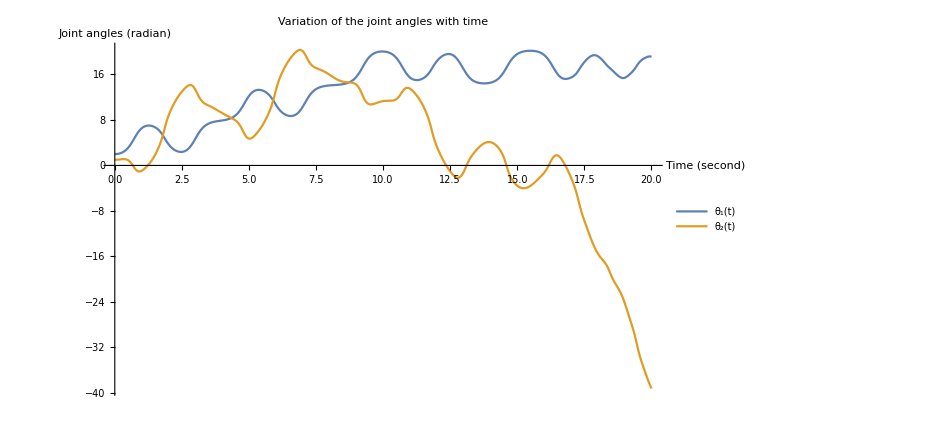

```mathematica
Plot[Evaluate[{θ1[t], θ2[t]}/.solnθ],{t,0,tf}, PlotRange-> All, PlotStyle->Thick, PlotLegends->{"θ_1(t)", "θ_2(t)"},LabelStyle->Directive[Bold,Black,15], AxesLabel-> {"Time (second)","Joint angles (radian)"}, PlotLabel->"Variation of the joint angles with time",ImageSize->700]
```

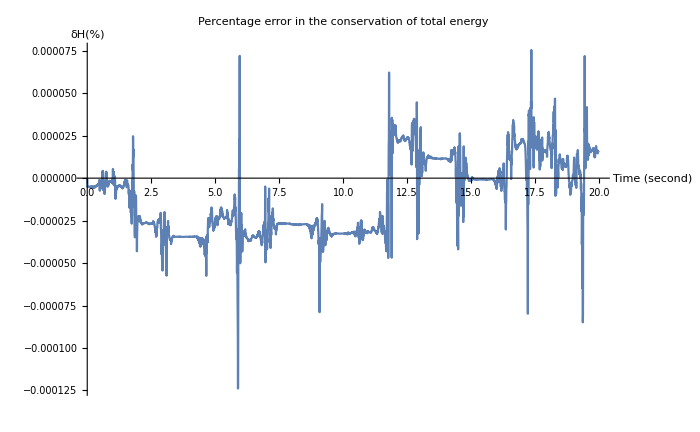

```mathematica
Plot[δH/.solnθ,{t,0,tf}, PlotRange-> All,LabelStyle->Directive[Bold, Black,15], AxesLabel-> {"Time (second)","δH(%)"}, PlotLabel->"Percentage error in the conservation of total energy",ImageSize->700]
```

```mathematica
cKE = KE/.{θ2'[t]->dT2, θ1'[t]->dT1, θ1[t]->t1, θ2[t]->t2}
```

{{0.5 (dT2 (dT2 (I2+m3 (l2^2 Cos[t1+t2]^2+l2^2 Sin[t1+t2]^2)+m2 (r2^2 Cos[t1+t2]^2+r2^2 Sin[t1+t2]^2))+dT1 (I2+m3 (l2 Cos[t1+t2] (l1 Cos[t1]+l2 Cos[t1+t2])-l2 Sin[t1+t2] (-l1 Sin[t1]-l2 Sin[t1+t2]))+m2 (r2 Cos[t1+t2] (l1 Cos[t1]+r2 Cos[t1+t2])-r2 Sin[t1+t2] (-l1 Sin[t1]-r2 Sin[t1+t2]))))+dT1 (dT2 (I2+m3 (l2 Cos[t1+t2] (l1 Cos[t1]+l2 Cos[t1+t2])-l2 Sin[t1+t2] (-l1 Sin[t1]-l2 Sin[t1+t2]))+m2 (r2 Cos[t1+t2] (l1 Cos[t1]+r2 Cos[t1+t2])-r2 Sin[t1+t2] (-l1 Sin[t1]-r2 Sin[t1+t2])))+dT1 (I1+I2+m1 (r1^2 Cos[t1]^2+r1^2 Sin[t1]^2)+m3 ((l1 Cos[t1]+l2 Cos[t1+t2])^2+(-l1 Sin[t1]-l2 Sin[t1+t2])^2)+m2 ((l1 Cos[t1]+r2 Cos[t1+t2])^2+(-l1 Sin[t1]-r2 Sin[t1+t2])^2))))}}

```mathematica
ToMatlab[cKE]
```

[0.5E0.*(dT2.*(dT2.*(I2+m3.*(l2.^2.*cos(t1+t2).^2+l2.^2.*sin(t1+ ...
  t2).^2)+m2.*(r2.^2.*cos(t1+t2).^2+r2.^2.*sin(t1+t2).^2))+dT1.*(I2+ ...
  m3.*(l2.*cos(t1+t2).*(l1.*cos(t1)+l2.*cos(t1+t2))+(-1).*l2.*sin( ...
  t1+t2).*((-1).*l1.*sin(t1)+(-1).*l2.*sin(t1+t2)))+m2.*(r2.*cos(t1+ ...
  t2).*(l1.*cos(t1)+r2.*cos(t1+t2))+(-1).*r2.*sin(t1+t2).*((-1).* ...
  l1.*sin(t1)+(-1).*r2.*sin(t1+t2)))))+dT1.*(dT2.*(I2+m3.*(l2.*cos( ...
  t1+t2).*(l1.*cos(t1)+l2.*cos(t1+t2))+(-1).*l2.*sin(t1+t2).*((-1).* ...
  l1.*sin(t1)+(-1).*l2.*sin(t1+t2)))+m2.*(r2.*cos(t1+t2).*(l1.*cos( ...
  t1)+r2.*cos(t1+t2))+(-1).*r2.*sin(t1+t2).*((-1).*l1.*sin(t1)+(-1) ...
  .*r2.*sin(t1+t2))))+dT1.*(I1+I2+m1.*(r1.^2.*cos(t1).^2+r1.^2.*sin( ...
  t1).^2)+m3.*((l1.*cos(t1)+l2.*cos(t1+t2)).^2+((-1).*l1.*sin(t1)+( ...
  -1).*l2.*sin(t1+t2)).^2)+m2.*((l1.*cos(t1)+r2.*cos(t1+t2)).^2+(( ...
  -1).*l1.*sin(t1)+(-1).*r2.*sin(t1+t2)).^2))))];